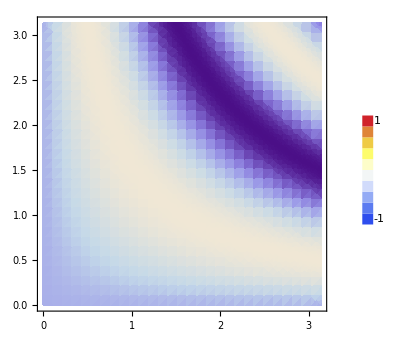

```mathematica
ShowLegend[DensityPlot[Sin[x y],{x,0,π},{y,0,π},Mesh->False,PlotPoints->30],{ColorData["TemperatureMap"][1-#1]&,10," 1","-1",LegendPosition->{1.1,-.4}}]
```

```mathematica
Max[Sin[x y], {{x,0,π},{y,0,π}}]
```

Max[π,x,y,Sin[x y]]

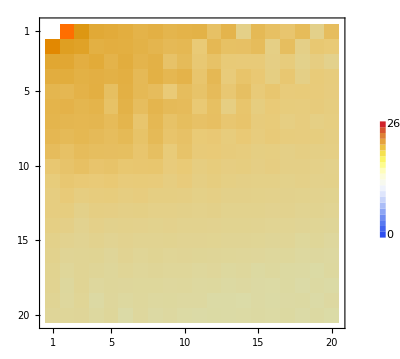

```mathematica
dftCorner0=
ShowLegend[
MatrixPlot[FData[[1;;20,1;;20]], BaseStyle->{FontWeight->"Plain",FontSize->25}],{ColorData["TemperatureMap"][1-#1]&,20,"26","0",LegendPosition->{1.1,-.4}}
]
```

```mathematica
FData[[1;;5,1;;5]]
```

{{0,26.6185,6.54197,1.32902,0.862353},{12.3854,4.09068,3.39286,0.208909,0.340049},{1.86011,1.79171,0.294318,0.930939,0.13115},{0.402539,0.448201,0.176836,0.240318,0.162534},{0.107348,0.0917102,0.13862,0.278679,0.0561954}}

```mathematica
f={{0,26.6185,6.54197,1.32902,0.862353},{12.3854,4.09068,3.39286,0.208909,0.340049},{1.86011,1.79171,0.294318,0.930939,0.13115},{0.402539,0.448201,0.176836,0.240318,0.162534},{0.107348,0.0917102,0.13862,0.278679,0.0561954}}
```

{{0,26.6185,6.54197,1.32902,0.862353},{12.3854,4.09068,3.39286,0.208909,0.340049},{1.86011,1.79171,0.294318,0.930939,0.13115},{0.402539,0.448201,0.176836,0.240318,0.162534},{0.107348,0.0917102,0.13862,0.278679,0.0561954}}

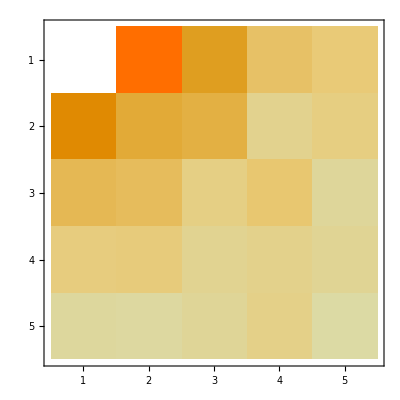

```mathematica
MatrixPlot[f]
```

```mathematica
ToString[Max[f]]
```

26.6185

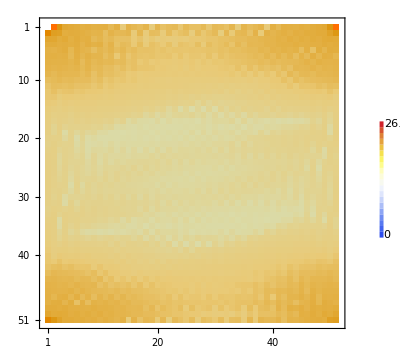

```mathematica
ShowLegend[
MatrixPlot[FData, BaseStyle->{FontWeight->"Plain",FontSize->25}],{ColorData["TemperatureMap"][1-#1]&,20,ToString[Max[f]],ToString[Min[f]],LegendPosition->{1.1,-.4}}
]
```

Part::partd: Part specification Round ⟦ 12 ⟧ is longer than depth of object.

Extract::psl: Position specification Round ⟦ 12 ⟧ in Extract[{{0, 26.6185, 6.54197, 1.32902, 0.862353}, {12.3854, 4.09068, 3.39286, 0.208909, 0.340049}, {1.86011, 1.79171, 0.294318, 0.930939, 0.13115}, {0.402539, 0.448201, 0.176836, 0.240318, 0.162534}, {0.107348, 0.0917102, 0.13862, 0.278679, 0.0561954}}, Round ⟦ 12 ⟧] is not an integer or a list of integers.

Part::partd: Part specification Round ⟦ 17 ⟧ is longer than depth of object.

Extract::psl: Position specification Round ⟦ 17 ⟧ in Extract[{{0.31092, 0.315997, 0.703565, 0.00702456, 0.159434, 0.93093, 0.673605, 0.0771913, 0.0644927, 0.273441}, « 8 », {0.802857, « 8 », 0.0751561}}, Round ⟦ 17 ⟧] is not an integer or a list of integers.

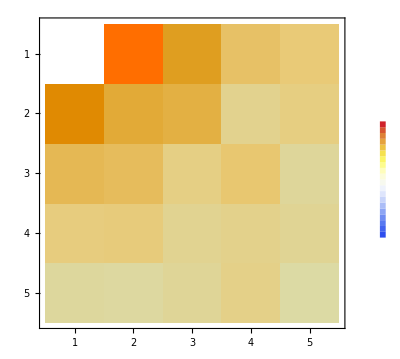

```mathematica
max=Position[colorvals,Max@colorvals][[1,1]];
min=Position[colorvals,Min@colorvals][[1,1]];
vals={Extract[f,Round[[max]]],Extract[data,Round[[min]]]};
minval=ToString@Round[Min@vals,0.1];
maxval=ToString@Round[Max@vals,0.1];
ShowLegend[
MatrixPlot[f, BaseStyle->{FontWeight->"Plain",FontSize->25}],{ColorData["TemperatureMap"][1-#1]&,20,maxval,minval,LegendPosition->{1.1,-.4}}
]
```

```mathematica
data=RandomReal[{0,1},{10,10}];
plot=ListDensityPlot[data,PlotRange->Automatic,ColorFunction->GrayLevel];
coords=List@@InputForm[plot][[1,1,1]];
colorvals=List@@InputForm[plot][[1,1,3,2]];
max=Position[colorvals,Max@colorvals][[1,1]];
min=Position[colorvals,Min@colorvals][[1,1]];
vals={Extract[data,Round[coords[[max]]]],Extract[data,Round[coords[[min]]]]};
minval=ToString@Round[Min@vals,0.1];
maxval=ToString@Round[Max@vals,0.1];
```

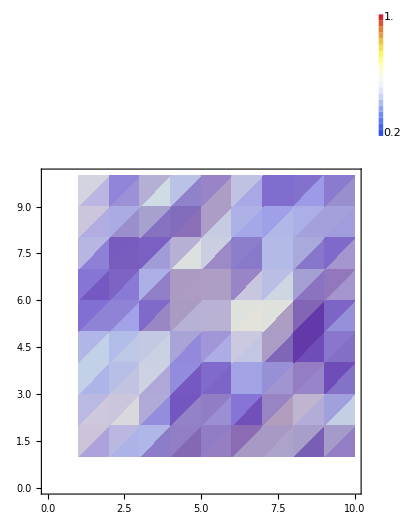

```mathematica
ShowLegend[ListDensityPlot[data,PlotRange->Automatic],{ColorData["TemperatureMap"][1-#1]&,20,maxval,minval,LegendPosition->{1,1}}]
```